```mathematica
Лабораторная работа №5
Ковальчук Владислав, ПО-4
```

```mathematica
Задание 1:
```

```mathematica
а) Пробел выполняет роль знака умножения:
```

```mathematica
3 5
```

15

```mathematica
б)Введение дополнительных пробелом неизменяютрезультата вычислений:
```

```mathematica
3  5
```

15

```mathematica
2+          7
```

9

```mathematica
в) Целые, рациональные и иррациональные числа считаются заданными точно. Поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя.
```

```mathematica
2 / 3
```

2/3

```mathematica
17 ^ (1 / 2)
```

√17

```mathematica
г) Действительные числа, содержащие десятичную точку, считаются заданными приближенно. Поэтому выражения, в которые входят действительные числа, вычисляются при обработке секции без специальной команды
```

```mathematica
3 / 7.
```

0.428571

```mathematica
17. ^ (1/2)
```

4.12311

```mathematica
д) Для изменения стандартного порядка выполнения операций используются скобки
```

```mathematica
5 (4 -1)
```

15

```mathematica
Задание 2:
```

```mathematica
а) С помощью функции N вычислить 17^(1/2) с точностью до 200 значащих цифр.Провериться потом с помощью Precision
```

```mathematica
N[Sqrt[17], 200]
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[%] (* % - ссылка на полученные ранее результаты *)
```

200.

```mathematica
б)Найти приближенное значение числа с точностью до 40 значащих цифр.Вычислить насколько полученный результат отличается от ближайшего к нему целого числа
```

```mathematica
N[E^(Pi*Sqrt[163]),40]
```

2.625374126407687439999999999992500725972×10^17

```mathematica
Round[N[E^(Pi*Sqrt[163]),40]] - N[E^(Pi*Sqrt[163]),40]
```

7.499274028×10^-13

```mathematica
в) Вычислить
```

```mathematica
(10*((10.8*10^3)/300)^(1/2) + 4)^(1/3)
```

4.

```mathematica
(10^-24 10^12)/10^-14 √(32768/2^9)
```

800

```mathematica
г) Последовательно введите выражения|Справедливо ли неравенство
```

```mathematica
5>3
```

True

```mathematica
5<2
```

False

```mathematica
Pi^E>E^Pi
```

False

```mathematica
N[Pi^E]
```

22.4592

```mathematica
N[E^Pi]
```

23.1407

```mathematica
Задание 3:
```

```mathematica
а) Решить уравнения
```

```mathematica
NSolve[Sqrt[x+2]+4 * x == 4,x]
```

{{x→0.597111}}

```mathematica
NSolve[x^3-3  x^2+5 == 0, x]
```

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

```mathematica
б) Решить системы уравнений
```

```mathematica
NSolve[{x^2+x*y+y^2==1,x^3+x^2*y+x*y^2+y^3==4},{x,y}]
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{x-y^2+3*z==34,x+y-z==-1,-x+2*y+3*z==4},{x,y,z}]
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

```mathematica
в) Придумать уравнение или систему уравнений и найдите её численное решение
```

```mathematica
NSolve[{x^3+y^3+3*x^2*y+3*y^2*x==64,x+3*y==8}, {x,y}, Reals]
```

{{x→2.,y→2.}}

```mathematica
Задание 4:
```

```mathematica
Вариант 12
E^-x = sin(2x) на отрезке x =>{0, 4}
```

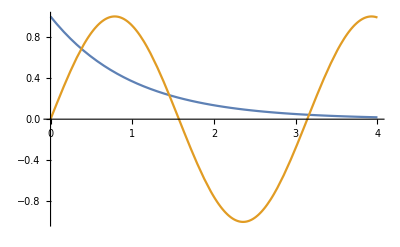

```mathematica
Plot[{E^-x, Sin[2x]}, {x, 0,4}]
```

```mathematica
x1 = .4; x2 = 1.5; x3 = 3.2;
```

```mathematica
FindRoot[E^-x == Sin[2x], {x, x1}]
```

{x→0.377633}

```mathematica
FindRoot[E^-x == Sin[2x], {x, x2}]
```

{x→1.45274}

```mathematica
FindRoot[E^-x == Sin[2x], {x, x3}]
```

{x→3.16275}

```mathematica
Задание 5:
```

```mathematica
Вариант 12
y''+0.5y'+(1+cos(x))y=0, y(0)=0, y'(0)=-1 на отрезке x=>[0,8]
```

```mathematica
result = NDSolve[{y''[x]+0.5y'[x]+(1+Cos[x])y[x]==0, y[0]==0, y'[0]==-1}, y, {x, 0, 8}]
```

{{y→InterpolatingFunction[…]}}

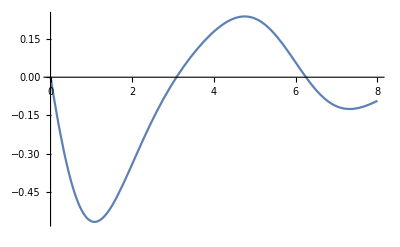

```mathematica
Plot[y[x]/. result, {x, 0, 8}]
```

```mathematica
а)Найдите на заданном отрезке корни уравнения y(x)=0
```

```mathematica
r1 = FindRoot[y[x]/.result, {x, 3}]
```

{x→3.08087}

```mathematica
r2 = FindRoot[y[x]/.result,{x, 6.25}]
```

{x→6.25026}

```mathematica
б) Найдите значения производной y'(x) в точках,где y(x)=0
```

```mathematica
D[y[x]/.result,x]/.r1
```

{0.247129}

```mathematica
D[y[x]/.result,x]/.r2
```

{-0.220448}

```mathematica
в) Выберите одну из точек,в которых производная функции y(x)=0,и вычислите значение функции в этой точке
```

```mathematica
LocalMinimum = FindRoot[D[y[x]/.result,x]==0,{x, 1.2}](*Производная равна 0 в точках, где касательная к графику функции паралельна оси абсцисс(точки экстремума)*)
```

{x→1.07626}

```mathematica
y[x]/.result/.LocalMinimum
```

{-0.568429}

```mathematica
г) С помощью функции FindMinimum найдите точки,в которых функция y(x) имеет локальный минимум или максимум,и сравните полученные результаты со значениями,найденными в пункте'в'
```

```mathematica
FindMinimum[y[x]/.result,{x, 1.2}]
```

{-0.568429,{x→1.07626}}

```mathematica
Задание 6:
```

```mathematica
а) Задайте произвольные численные значения параметров a,b,c,d,e в следующих зависимостях:y(x)=a+b*x+c*x^2+d*x^3+e*x^4 и y(x)=a+b*x+c*sin(x)+d*cos(x).Используя функцию Table,определите список численных данных,каждый элемент которого содержит два элемента (x,y).Область изменения х и шаг выберите самостоятельно.С помощью функции Random внесите в каждой точке х случайное возмущение Дy
```

```mathematica
1)
```

```mathematica
dat1=Table[{x,(10+8*x+6*x^2+4*x^3+2*x^4)(1+Random[Real,{-0.1,0.1}])},{x,0,4,0.2}]
```

{{0.,10.8845},{0.2,11.2102},{0.4,14.7633},{0.6,18.0838},{0.8,24.3377},{1.,31.9058},{1.2,36.8316},{1.4,53.7167},{1.6,73.1782},{1.8,86.2344},{2.,105.859},{2.2,148.208},{2.4,168.411},{2.6,216.841},{2.8,267.718},{3.,375.036},{3.2,474.82},{3.4,508.36},{3.6,577.647},{3.8,696.756},{4.,988.191}}

```mathematica
2)
```

```mathematica
dat2=Table[{x,(20+38*x+62*Sin[x]+25*Cos[x])(1+Random[Real,{-0.1,0.1}])},{x,0,5,0.2}]
```

{{0.,46.3762},{0.2,61.4214},{0.4,86.5222},{0.6,88.8201},{0.8,110.787},{1.,127.76},{1.2,125.872},{1.4,131.483},{1.6,145.318},{1.8,142.495},{2.,143.355},{2.2,134.471},{2.4,127.229},{2.6,125.096},{2.8,135.38},{3.,113.162},{3.2,103.362},{3.4,103.138},{3.6,101.341},{3.8,103.971},{4.,114.961},{4.2,106.595},{4.4,112.694},{4.6,128.274},{4.8,132.349},{5.,171.401}}

```mathematica
б)Изобразите полученные точки на координатной плоскости
```

```mathematica
1)
```

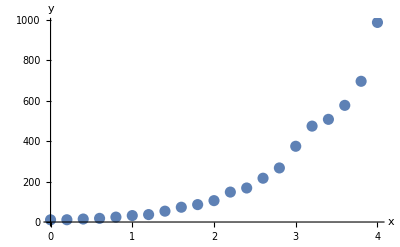

```mathematica
y1=ListPlot[dat1,PlotStyle->PointSize[0.02],AxesLabel->{"x","y"}]
```

```mathematica
2)
```

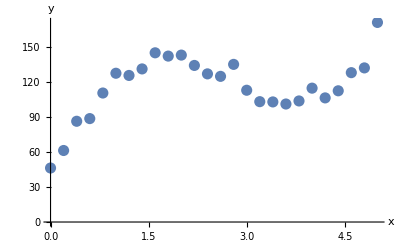

```mathematica
p1=ListPlot[dat2,PlotStyle->PointSize[0.02],AxesLabel->{"x","y"}]
```

```mathematica
в) С помощью функции Fit найдите наилучшую кривую,аппроксимирующую численные данные
```

```mathematica
1)
```

```mathematica
apr1=Fit[dat1,{1,x,x^2,x^3,x^4},x] (* Чтобы найти наилучшее, с точки зрения метода нименьших квадратов, значение коэффициентов в выражении, используется функция Fit. Первый аргумент - список численных данных, второй - список функций, линейная комбинация которых должна аппроксимировать искомую зависимость. *)
```

18.0555-54.5895 x+94.2739 x^2-36.3097 x^3+7.60207 x^4

```mathematica
apr2=Fit[dat1,{1,x,Sin[x]},x]
```

58.1179+132.233 x-239.787 Sin[x]

```mathematica
2)
```

```mathematica
aproc1=Fit[dat2,{1,x,Sin[x],Cos[x]},x]
```

14.794+39.3366 x+27.8115 Cos[x]+63.8001 Sin[x]

```mathematica
aproc2=Fit[dat2,{1,x,x^2,x^3},x]
```

36.384+144.117 x-62.4788 x^2+7.71346 x^3

```mathematica
г) На одной координатной плоскости изобразите найденную кривую вместе с экспериментальными точками
```

```mathematica
1)
```

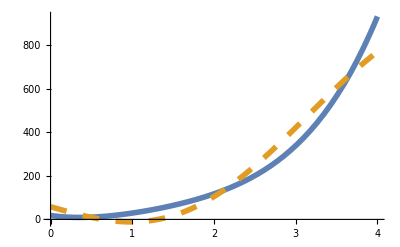

```mathematica
y2=Plot[{apr1,apr2},{x,0,4},
PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

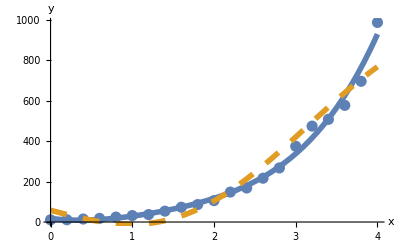

```mathematica
Show[y1,y2]
```

```mathematica
2)
```

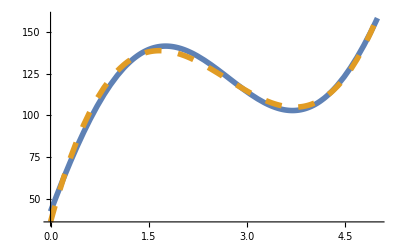

```mathematica
p2=Plot[{aproc1,aproc2},{x,0,5},
PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

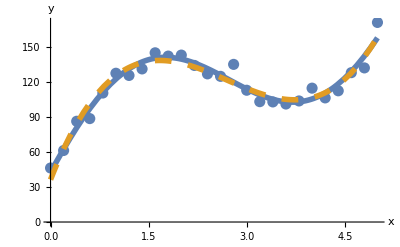

```mathematica
Show[p1,p2]
```